```mathematica
rawOld=Import["/Users/nmajik/Documents/SLAC/slacsyncgit/bmadExample/bmad/beams/L0AFEND_matched.h5","Data"];
```

```mathematica
rawOld//Keys
```

{/momentum/x,/momentum/y,/momentum/z,/position/x,/position/y,/time}

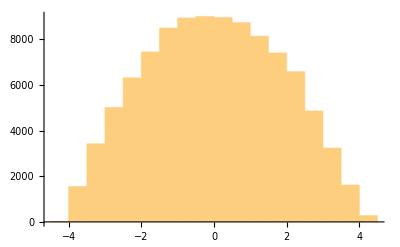

```mathematica
rawOld["/time"]//Histogram
```

```mathematica
rawNew=Import["/Users/nmajik/Documents/SLAC/slacsyncgit/bmadExample/bmad/beams/nmmToL0AFEND_2bunch_2024-02-16Clean/2024-02-16_2bunch.h5","Data"];
```

```mathematica
rawNew//Keys
```

{/id,/momentum/x,/momentum/y,/momentum/z,/position/x,/position/y,/position/z,/time,/weight}

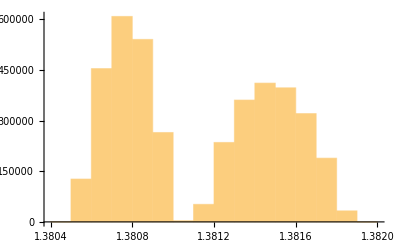

```mathematica
rawNew["/time"]//Histogram
```

```mathematica
Mean[rawNew["/time"]]*cN
```

4.14052

Yup, my beam is not centered at t = 0

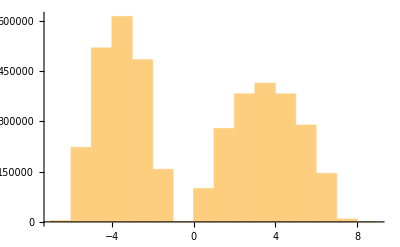

```mathematica
rawNew["/time"]-Mean[rawNew["/time"]]//Histogram
```

```mathematica
rawNewNew=Import["/Users/nmajik/Documents/SLAC/slacsyncgit/bmadExample/bmad/beams/activeBeamFile.h5","Data"];
```

```mathematica
rawNewNew["/time"]//Histogram
```

-Graphics-

```mathematica
Mean[rawNewNew["/time"]]*cN
```

1.57312×10^-15